{{y→Function[{t},Cos[√2 t]-ⅈ Sin[√2 t]]}}

{{y→InterpolatingFunction[…]}}

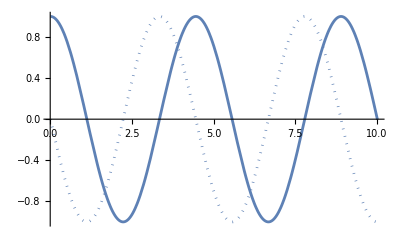

-Graphics-

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]

k := 1
m := 1
omega := Sqrt[k^2+m^2]

eps := 0.01
Tmax := 10.01
(*ysol=NDSolve[{y''[t]+omega^2 y[t] == 0, y[eps]==1, y[Tmax]==Exp[-I*omega*Tmax]},y,{t,eps,Tmax}]*)

symsol = DSolve[{y''[t]+omega^2 y[t] == 0, y[0]==1, y'[0]==-I*omega}, y, t]

numsol=NDSolve[{y''[t]+omega^2 y[t] == 0, y[eps]==1, y'[eps]==-I*omega},y,{t,eps,Tmax}]

ReImPlot[Evaluate[y[t]/. numsol],{t,eps,Tmax},PlotRange->All]
AbsArgPlot[Evaluate[y[t]/. numsol],{t,eps,Tmax},PlotRange->{{0, Tmax},{0, 2}}]
```